```mathematica
(*截面上的场强*)
```

```mathematica
By[y_,z_]:=(1/((d/2-y)^2+z^2)-1/((d/2+y)^2+z^2))*z;
Bz[y_,z_]:=(d/2-y)/((d/2-y)^2+z^2)+(d/2+y)/((d/2+y)^2+z^2);
d=2;
Plot[Bz[0,z],{z,-3d,3d},AxesLabel->{"z","Bz"}]
Plot[Bz[y,d/2],{y,-3d,3d},AxesLabel->{"y","Bz"}]
Plot[By[y,d/2],{y,-3d,3d},AxesLabel->{"y","Bz"}]
Plot3D[By[y,z],{y,-3d,3d},{z,-3d,3d},PlotRange->All,PlotPoints->100,Mesh->False,AxesLabel->{"y","z","By"}]
```

-Graphics-

-Graphics-

-Graphics-

-Graphics3D-

```mathematica
Clear[By,Bz,d]
```

```mathematica
(*截面上的B线，折线法*)
```

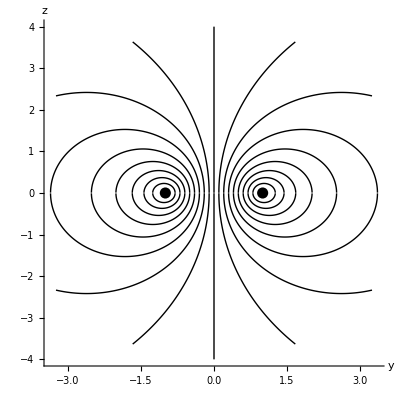

```mathematica
By[y_,z_]:=(1/((d/2-y)^2+z^2)-1/((d/2+y)^2+z^2))*z;
Bz[y_,z_]:=(d/2-y)/((d/2-y)^2+z^2)+(d/2+y)/((d/2+y)^2+z^2);
d=2.0;r1=step=0.005;r2=2d;forceline={};
Do[θ=π/2.0;p={y0,r1};single={};
While[(Abs[p[[2]]]≥r1)∧(Norm[p]<r2),
AppendTo[single,p];p=p+step*{Cos[θ],Sin[θ]};
θ=Arg[By[p[[1]],p[[2]]]+ⅈ*Bz[p[[1]],p[[2]]]]];
AppendTo[forceline,single];m=Length[single];
single=Table[{single[[j,1]],-single[[j,2]]},{j,m}];
AppendTo[forceline,single],{y0,-0.8d/2,0.8d/2,0.1d/2}]
Show[Graphics[{Line/@forceline}],Axes->True,AxesLabel->{"y","z"},AspectRatio->1,Epilog->{PointSize[0.02],Point/@{{d/2,0},{-d/2,0}}}]
```